# Analytical calculations for M, K varied (cont. time limit)

## 1. Computing changes in frequency due to selection (p < 1)

### Introduction

In this notebook, we aim to compute the change in each strategy due to selection <Δx_s^sel> in the case p < 1.
From the SI, the quantities of interest in the limit of weak selection (β->0) are:

<Δ(x^sel)_CC> = β<1/n^2∑_i s_{i,a}s_{i,d} Z_i> =β<Δ(x^sel)_CC>_0,                    <Δ(x^sel)_CD> =β<1/n^2∑_i s_{i,a}(1-s_{i,d})Z_i> =β<Δ(x^sel)_CD>_0,         
<Δ(x^sel)_DC> = β<1/n^2∑_i (1-s_{i,a})s_{i,d}Z_i> = β<(Δx^sel)_DC>_0,        <Δ(x^sel)_DD> = β<1/n^2∑_i (1-s_{i,a})(1-s_{i,d})Z_i> =β<Δ(x^sel)_DD>_0

where the brackets indicate averages taken over the stationary distribution in the neutral state.

### Defining payoffs

The general payoff function is given by

π_i=-K s_{i,a}(b-c)+1/2 ∑_(l=1)^n ∑_(k=1)^m|h_ik h_lk |(b h_ik h_lk (s_{l,a}-s_{l,d})+b (s_{l,a}+s_{l,d})-c h_ik h_lk (s_{i,a}-s_{i,d})-c (s_{i,a}+s_{i,d}))

Thought not required in the calculation, we first define the payoff function for each strategy so that we can simplify the expressions more easily. Note that we use small n instead of N to avoid confusion with the Mathematica function N.

```mathematica
Clear["Global`*"]
```

```mathematica
πgeneral[i_]:= -K*(Subscript[s, {i,a}])(b-c) + 1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[ Subscript[h, {i,k}] Subscript[h, {l,k}]]ExpandAll[(-c (Subscript[s, {i,a}]+Subscript[s, {i,d}])+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, {i,k}] Subscript[h, {l,k}](Subscript[s, {i,a}]-Subscript[s, {i,d}])+b Subscript[h, {i,k}] Subscript[h, {l,k}] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
πstrat[i_,sia_,sid_]:= (*sia,sid∈{0,1} to indicate strategy*)-K*(sia)(b-c) + 1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[ Subscript[h, {i,k}] Subscript[h, {l,k}]]ExpandAll[(-c (sia+sid)+b  (Subscript[s, {l,a}]+Subscript[s, {l,d}])-c Subscript[h, {i,k}] Subscript[h, {l,k}](sia-sid)+b Subscript[h, {i,k}] Subscript[h, {l,k}] (Subscript[s, {l,a}]-Subscript[s, {l,d}]))]
```

```mathematica
πCC[i_]:=πstrat[i,1,1]
πCD[i_]:=πstrat[i,1,0] 
πDC[i_]:=πstrat[i,0,1]
πDD[i_]:=πstrat[i,0,0]
```

We also define the quantity Z_i (see above):

```mathematica
Z[πstrat_,i_,n_]:=πstrat[i]-1/n∑_(j=1)^n πgeneral[j]//ExpandAll
```

The strategy-specific payoffs are

```mathematica
πCC[i]
πCD[i]
πDC[i]
πDD[i]
```

-(b-c) K+1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[h_{i,k} h_{l,k}] (-2 c+b s_{l,a}+b h_{i,k} h_{l,k} s_{l,a}+b s_{l,d}-b h_{i,k} h_{l,k} s_{l,d})

-(b-c) K+1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[h_{i,k} h_{l,k}] (-c-c h_{i,k} h_{l,k}+b s_{l,a}+b h_{i,k} h_{l,k} s_{l,a}+b s_{l,d}-b h_{i,k} h_{l,k} s_{l,d})

1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[h_{i,k} h_{l,k}] (-c+c h_{i,k} h_{l,k}+b s_{l,a}+b h_{i,k} h_{l,k} s_{l,a}+b s_{l,d}-b h_{i,k} h_{l,k} s_{l,d})

1/2 ∑_(l=1)^n ∑_(k=1)^M RealAbs[h_{i,k} h_{l,k}] (b s_{l,a}+b h_{i,k} h_{l,k} s_{l,a}+b s_{l,d}-b h_{i,k} h_{l,k} s_{l,d})

### Defining rules

Next, we define some rules to simplify the summations:

```mathematica
(*rules for initial simplification*)
sumRule=Sum[expr1_,iter_]+Sum[expr2_,iter_]:>Sum[expr1+expr2,iter];
prodRule=Sum[expr1_,iter1_]*Sum[expr2_,iter2_]:>Sum[expr1*expr2,iter1,iter2];
revSumRule=Sum[expr1_+expr2_,iter_]:> Sum[expr1,iter]+Sum[expr2,iter];
constRule=Sum[c_?NumericQ  expr_,iter_]:>c Sum[expr,iter];
distRule=a_(b_+c_):>a*b+a*c;
dist2Rule=s_Subscript(b_+c_):>s*b+s*c;

miscRule=s_Subscript Sum[expr_,iter_]:> Sum[s*expr,iter];
squareRule = s_Subscript^2:>s;
unbracketRule=Sum[expr_,{i_,1,n_}]:> n expr;
unbracketRule2=Sum[expr_,{l_,1,m_},{i_,1,n_}]:> m n expr;

(*rules for collecting terms*)
mergeRule=a_ s1_Subscript s2_Subscript+b_ s1_Subscript s2_Subscript:> (FullSimplify[a+b])s1 s2;
```

### Simplifying expressions

To make calculations easier, we will first compute terms in (3) divided by β (i.e., <Δ(x^sel)_s>_0):

```mathematica
expandBracket[bracket_]:=ExpandAll[bracket]/.revSumRule/.constRule/.distRule//.miscRule//.distRule //.squareRule//.sumRule//.unbracketRule//.unbracketRule2
```

```mathematica
xCCbracket:=expandBracket[1/n Subscript[s, {i,a}] Subscript[s, {i,d}] Z[πCC,i,n]] // FullSimplify//ExpandAll
xCDbracket:=expandBracket[1/n Subscript[s, {i,a}](1-Subscript[s, {i,d}])Z[πCD,i,n]] //FullSimplify//ExpandAll
xDCbracket:=expandBracket[1/n(1-Subscript[s, {i,a}])Subscript[s, {i,d}] Z[πDC,i,n]]// FullSimplify//ExpandAll
xDDbracket:=expandBracket[1/n(1-Subscript[s, {i,a}])(1-Subscript[s, {i,d}])Z[πDD,i,n]]  // FullSimplify//ExpandAll
```

```mathematica
(*Check above values*)
(*xCCbracket*)
(*xCDbracket*)
(*xDCbracket*)
(*xDDbracket*)
```

#### Simplifying the CC term

First, we define rules for relabeling quantities that are equivalent (note that the order of substitution matters here).

```mathematica
subCC0={RealAbs[Subscript[h, {j_,k}] Subscript[h, {l_,k}]] Subscript[h, {j_,k}] Subscript[h, {l_,k}] :> Subscript[h, {j,k}] Subscript[h, {l,k}]};
subCC1={Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}],
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2 Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,a}],
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}],
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,a}],
             Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}],     
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}]  Subscript[s, {l,a}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}],
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> 1/2 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> 1/2 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> 1/2 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}],
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> 1/2 RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}]};
subCC2={Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)),
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)),
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n gp),
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 hp+(n-1)/n^2(zp+gp+y)),
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 hp+(n-1)/n^2(zp+gp+y))};
subCC3={Subscript[s, {i,a}] Subscript[s, {i,d}] Subscript[s, {j,a}]:>1/2 Subscript[s, {i,a}] Subscript[s, {j,a}],
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}]:> 1/4(1/n+(n-1)/n zp)};
subCC4={Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4,
             Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y)};
subCC5={Subscript[s, {i,d}]-> 1/2};
```

Then we can simplify the expression for CC as:

```mathematica
xCCbracket2=xCCbracket//.distRule//.subCC0//.subCC1//.subCC2//.subCC3//.subCC4//.subCC5//FullSimplify
```

((-1+n) (b (K (-1+y)-M (-1+gp+hp (-2+n)-gp n+y+zp))+c (K-K y+M (-1+gp+hp (-2+n)+y+zp-n zp))))/(4 n^2)

In the limit n→∞, we can further simplify this expression:

```mathematica
xCCbracket3=FullSimplify[xCCbracket//.distRule//.subCC0//.subCC1//.subCC2//.subCC3//.subCC4//.subCC5 ]/.{n-1->n,n-2->n}//.{g_-g_ n+h_ n+z_->-g n+h n}//.{-M (-gp n+hp n)+K (-1+y)->-M (-gp n+hp n),K-K y+M (hp n-n zp)->M (hp n-n zp)}//FullSimplify
```

1/4 M (b (gp-hp)+c (hp-zp))

#### Simplifying the CD term

```mathematica
subCD6={Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 Subscript[h, {j,k}] Subscript[h, {l,k}],
             Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 Subscript[h, {i,k}] Subscript[h, {l,k}],
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4 Subscript[h, {j,k}] Subscript[h, {l,k}],
             Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4 Subscript[h, {i,k}] Subscript[h, {l,k}],
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]],
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,d}]-> 1/4 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]], (*change of variables*)
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,d}]-> 1/4 RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]],
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4 RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] };
(*subCD7={Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n g),
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)),
             Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 h+(n-1)/n^2(z+g+y)) ,
             RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}]-> 1/2(1/n+(n-1)/n gp),
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}]->  1/2(1/n^2+((n-1)(n-2))/n^2 hp+(n-1)/n^2(zp+gp+yp)),
             RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n^2+((n-1)(n-2))/n^2 hp+(n-1)/n^2(zp+gp+yp))};*)
subCD7={RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]]-> 1/n+(n-1)/n zp,RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]]-> 1/n+(n-1)/n zp};
subCD8={Subscript[h, {i,k}] Subscript[h, {l,k}]-> 1/n+(n-1)/n z,Subscript[h, {j,k}] Subscript[h, {l,k}]-> 1/n+(n-1)/n z,
               Subscript[s, {i,a}] Subscript[s, {j,a}]-> 1/2(1/n+(n-1)/n y),Subscript[s, {i,a}] Subscript[s, {i,d}]-> 1/4};
subCD9={Subscript[s, {i,a}]-> 1/2,Subscript[s, {i,d}]-> 1/2};
```

```mathematica
xCDbracket2=FullSimplify[xCDbracket]//.distRule//.subCC0//.subCC1//.subCC2//.subCC3//.subCD6//.subCD7//.subCD8//.subCD9//FullSimplify
```

((-1+n) (b (K (-1+y)-M (-1+g+h (-2+n)-g n+y+z))+c (K-K y+M (-1+g+h (-2+n)+y+z-n z))))/(4 n^2)

```mathematica
(*infinit population limit*)
xCDbracket3=FullSimplify[xCDbracket//.distRule//.subCC0//.subCC1//.subCC2//.subCC3//.subCD6//.subCD7//.subCD8//.subCD9]/.{n-1->n,n-2->n}/.{-1+g-g n+h n+y+z -> -g n + h n,-1+g+h n+y+z-n z-> h n -n z} /.{ -M (-g n+h n)+K (-1+y)->-M (-g n+h n),K-K y+M (h n-n z)-> M (h n-n z)}//FullSimplify
```

1/4 M (b (g-h)+c (h-z))

#### Simplifying the DC term

```mathematica
subDC10={Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {j,a}]-> Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,d}],
                Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {j,d}]-> Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {j,a}],
                Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,d}],
                Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {l,a}]-> Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,d}],
                Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, {i,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}],
                Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,d}] Subscript[s, {l,d}]-> Subscript[h, {j,k}] Subscript[h, {l,k}] Subscript[s, {i,a}] Subscript[s, {l,a}],
                RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {j,a}]-> RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,d}],
                RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {j,d}]-> RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {j,a}],
                RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {l,a}]-> RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,d}],
                RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {l,a}]-> RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,d}],
                RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {l,d}]-> RealAbs[Subscript[h, {i,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}],
                RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,d}] Subscript[s, {l,d}]-> RealAbs[Subscript[h, {j,k}] Subscript[h, {l,k}]] Subscript[s, {i,a}] Subscript[s, {l,a}] };
subDC11={Subscript[s, {i,d}] Subscript[s, {j,a}]->1/4};
```

```mathematica
(*simplify*)
xDCbracket2=FullSimplify[xDCbracket]//.distRule//.subCC0//.subCC1//.subDC10//.subCD6//.subCC2//.subCC3//.subCD7//.subCD8//.subDC11//.subCD9//FullSimplify
```

-((-1+n) (b (K (-1+y)-M (-1+g+h (-2+n)-g n+y+z))+c (K-K y+M (-1+g+h (-2+n)+y+z-n z))))/(4 n^2)

```mathematica
(*infinit population limit*)xDCbracket3=FullSimplify[xDCbracket//.distRule//.subCC0//.subCC1//.subDC10//.subCD6//.subCC2//.subCC3//.subCD7//.subCD8//.subDC11//.subCD9]//.{n-1->n,n-2->n}/.{-1+g-g n+h n+y+z -> -g n + h n,-1+g+h n+y+z-n z-> h n -n z} /.{ -M (-g n+h n)+K (-1+y)->-M (-g n+h n),K-K y+M (h n-n z)-> M (h n-n z)}//FullSimplify
```

1/4 M (b (-g+h)+c (-h+z))

#### Simplifying the DD term

```mathematica
subDD12={Subscript[s, {j,a}]->1/2,Subscript[s, {j,d}]->1/2};
```

```mathematica
(*simplify*)
xDDbracket2=FullSimplify[xDDbracket]//.distRule//.subCC0//.subCC1//.subDC10//.subCD6//.subCC2//.subCC3//.subCD7//.subCD8//.subDC11//.subDD12//FullSimplify
```

-((-1+n) (b (K (-1+y)-M (-1+gp+hp (-2+n)-gp n+y+zp))+c (K-K y+M (-1+gp+hp (-2+n)+y+zp-n zp))))/(4 n^2)

```mathematica
(*infinit population limit*)
xDDbracket3=FullSimplify[xDDbracket//.distRule//.subCC0//.subCC1//.subDC10//.subCD6//.subCC2//.subCC3//.subCD7//.subCD8//.subDC11//.subDD12]/.{n-1->n,n-2->n}//.{g_-g_ n+h_ n+z_->-g n+h n}//.{-M (-gp n+hp n)+K (-1+y)->-M (-gp n+hp n),K-K y+M (hp n-n zp)->M (hp n-n zp)}//FullSimplify
```

1/4 M (b (-gp+hp)+c (-hp+zp))

### Summary

In the continuous time / large population limit, we have the following expressions for <Δx_CD^sel>_0=<Δ(x^sel)_s>/β:

```mathematica
Print["<Δx_CC^sel>_0= ",xCCbracket3,",  <Δx_CD^sel>_0= ",xCDbracket3,",  <Δx_DC^sel>_0 = ",xDCbracket3,",  <Δx_DD^sel>_0 = ",xDDbracket3]
```

<Δx_CC^sel>_0= 1/4 M (b (gp-hp)+c (hp-zp)),  <Δx_CD^sel>_0= 1/4 M (b (g-h)+c (h-z)),  <Δx_DC^sel>_0 = 1/4 M (b (-g+h)+c (-h+z)),  <Δx_DD^sel>_0 = 1/4 M (b (-gp+hp)+c (-hp+zp))

```mathematica
xCCbracket3+xCDbracket3+xDCbracket3+xDDbracket3 // FullSimplify (*should equal 0*)
```

0

## 2. Computing y, z, g, h in the continuous time limit for p < 1

To simplify the above expressions, we need to compute the quantities y, z, g, and h as defined in the SI.

### Define functions related to coalescence time

```mathematica
ρ[τ_,p_]:=Exp[-τ]
ρ2[τ3_,τ2_]:=3*Exp[-3*τ3]Exp[-τ2]
```

### Compute y

```mathematica
ytau[μ_,τ_,p_]:=1/2 (1+ⅇ^(-μ τ))(*from the SI*)
y[μ_,p_]:=Integrate[ytau[μ,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

We will also define a function to compute the integrals more quickly :

```mathematica
yeval[μ_,ν_]=y[μ,p];
ycalc[n_,u_,v_]=y[μ,p]/.{μ->n*u};
```

```mathematica
Print["y = ",yeval[μ,ν]," or ",ycalc[n,u,v]]
```

y = (2+μ)/(2+2 μ) or (2+n u)/(2+2 n u)

### Compute z

```mathematica
ztau[ν_,τ_,p_]:=(K/M)ⅇ^(-ν τ)
z[ν_,p_]:=Integrate[ztau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
zeval[μ_,ν_]=z[ν,p]// FullSimplify;
zcalc[n_,u_,v_]=z[ν,p]/.{ν->n*v} // FullSimplify;
```

```mathematica
Print["z = ",zeval[μ,ν]," or ",zcalc[n,u,v]]
```

z = K/(M+M ν) or K/(M+M n v)

```mathematica
(*Check*)
zeval[μ,ν]-K/M(1/(1+ν))==0//FullSimplify
```

True

### Compute g

```mathematica
gtau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*ztau[ν,τ,p]
g[μ_,ν_,p_]:=Integrate[gtau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
geval[μ_,ν_]=g[μ,ν,p]//FullSimplify// Apart;
gcalc[n_,u_,v_]=g[μ,ν,p]/.{ν->n*v,μ->n*u}//FullSimplify// Apart;
```

```mathematica
Print["Check: g(τ) = ",gtau[μ,ν,τ,p]]
Print["g = ",geval[μ,ν]," or ",gcalc[n,u,v]]
```

Check: g(τ) = (ⅇ^(-ν τ) (1+ⅇ^(-μ τ)) K)/(2 M)

g = K/(2 M (1+ν))+K/(2 M (1+μ+ν)) or K/(2 M (1+n v))+K/(2 M (1+n u+n v))

```mathematica
(*Check*)
geval[μ,ν]-K/M 1/2(1/(1+ν)+1/(1+μ+ν))==0//FullSimplify
```

True

### Compute h

```mathematica
htau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*ztau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3,p]+ytau[μ,τ3+τ2,p]*ztau[ν,τ3+τ2,p])
h[μ_,ν_,p_]:=Integrate[htau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ3,0,Infinity},{τ2,0,Infinity}][[1]]
```

```mathematica
heval[μ_,ν_]=h[μ,ν,p] // FullSimplify//Apart; (*slow*)
hcalc[n_,u_,v_]=h[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
Print["Check: h(τ_3,τ_2) = ",htau[μ,ν,τ3,τ2,p]]
Print["h = ",heval[μ,ν]," or ",hcalc[n,u,v]]
```

Check: h(τ_3,τ_2) = 1/3 ((ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ τ3)) K)/(2 M)+(ⅇ^(-ν τ3) (1+ⅇ^(-μ (τ2+τ3))) K)/(2 M)+(ⅇ^(-ν (τ2+τ3)) (1+ⅇ^(-μ (τ2+τ3))) K)/(2 M))

h = (3 K+K μ)/(2 M (2+μ) (1+ν))+K/(4 M (1+μ+ν))-(K μ (3+μ))/(4 M (1+μ) (2+μ) (3+μ+ν)) or (K (3+n u))/(2 M (2+n u) (1+n v))+K/(4 M (1+n u+n v))-(K n u (3+n u))/(4 M (1+n u) (2+n u) (3+n u+n v))

```mathematica
(*Check*)
FullSimplify[heval[μ,ν]-1/2 K/M((3 + μ)/((2+μ) (1+ν))+1/(2 (1+μ+ν))-(μ (3+μ))/(2 (1+μ) (2+μ) (3+μ+ν)))]
```

0

### Compute z’ (zp)

```mathematica
zptau[ν_,τ_,p_]:=(K/M)((K/M)+(1-K/M)ⅇ^(-ν τ))
zp[ν_,p_]:=Integrate[zptau[ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
zpeval[μ_,ν_]=zp[ν,p]// FullSimplify//Apart;
zpcalc[n_,u_,v_]=zp[ν,p]/.{ν->n*v} // FullSimplify//Apart;
```

```mathematica
Print["z' = ",zpeval[μ,ν]," or ",zpcalc[n,u,v]]
```

z' = K^2/M^2+(-K^2+K M)/(M^2 (1+ν)) or K^2/M^2+(-K^2+K M)/(M^2 (1+n v))

```mathematica
(*Check*)
zpeval[μ,ν]-K/M(K/M+(1-K/M)(1/(1+ν)))==0//FullSimplify
zpeval[μ,ν]-((K/M)^2+(1-K/M)zeval[μ,ν])==0//FullSimplify
```

True

True

### Compute g’ (gp)

```mathematica
gptau[μ_,ν_,τ_,p_]:=ytau[μ,τ,p]*zptau[ν,τ,p]
gp[μ_,ν_,p_]:=Integrate[gptau[μ,ν,τ,p]*ρ[τ,p], {τ,0,Infinity}][[1]]
```

```mathematica
gpeval[μ_,ν_]=gp[μ,ν,p]//FullSimplify// Apart;
gpcalc[n_,u_,v_]=gp[μ,ν,p]/.{ν->n*v,μ->n*u}//FullSimplify// Apart;
```

```mathematica
Print["Check: g'(τ) = ",gptau[μ,ν,τ,p]]
Print["g' = ",gpeval[μ,ν]," or ",gpcalc[n,u,v]]
```

Check: g'(τ) = ((1+ⅇ^(-μ τ)) K (ⅇ^(-ν τ) (1-K/M)+K/M))/(2 M)

g' = (K^2 (2+μ))/(2 M^2 (1+μ))-(K (K-M))/(2 M^2 (1+ν))-(K (K-M))/(2 M^2 (1+μ+ν)) or (K^2 (2+n u))/(2 M^2 (1+n u))-(K (K-M))/(2 M^2 (1+n v))-(K (K-M))/(2 M^2 (1+n u+n v))

```mathematica
(*Check*)
gpeval[μ,ν]-1/2 K/M(K/M(2+μ)/(1+μ)+(1-K/M)(1/(1+ν)+1/(1+μ+ν)))==0//FullSimplify
gpeval[μ,ν]-((K/M)^2 yeval[μ,ν]+(1-K/M)geval[μ,ν])==0//FullSimplify
```

True

True

### Compute h’ (hp)

```mathematica
hptau[μ_,ν_,τ3_,τ2_,p_]:=1/3(ytau[μ,τ3,p]*zptau[ν,τ3+τ2,p]+ytau[μ,τ3+τ2,p]*zptau[ν,τ3,p]+ytau[μ,τ3+τ2,p]*zptau[ν,τ3+τ2,p])
hp[μ_,ν_,p_]:=Integrate[hptau[μ,ν,τ3,τ2,p]*ρ2[τ3,τ2], {τ3,0,Infinity},{τ2,0,Infinity}][[1]]
```

```mathematica
hpeval[μ_,ν_]=hp[μ,ν,p] // FullSimplify//Apart; (*slow*)
hpcalc[n_,u_,v_]=hp[μ,ν,p]/.{ν->n*v,μ->n*u} // FullSimplify// Apart;
```

```mathematica
Print["Check: h'(τ_3,τ_2) = ",hptau[μ,ν,τ3,τ2,p]]
Print["h' = ",hpeval[μ,ν]," or ",hpcalc[n,u,v]]
```

Check: h'(τ_3,τ_2) = 1/3 (((1+ⅇ^(-μ (τ2+τ3))) K (ⅇ^(-ν τ3) (1-K/M)+K/M))/(2 M)+((1+ⅇ^(-μ τ3)) K (ⅇ^(-ν (τ2+τ3)) (1-K/M)+K/M))/(2 M)+((1+ⅇ^(-μ (τ2+τ3))) K (ⅇ^(-ν (τ2+τ3)) (1-K/M)+K/M))/(2 M))

h' = (K^2 (2+μ))/(2 M^2 (1+μ))+(-3 K^2+3 K M-K^2 μ+K M μ)/(2 M^2 (2+μ) (1+ν))+(-K^2+K M)/(4 M^2 (1+μ+ν))+(3 K^2 μ-3 K M μ+K^2 μ^2-K M μ^2)/(4 M^2 (1+μ) (2+μ) (3+μ+ν)) or (K^2 (2+n u))/(2 M^2 (1+n u))+(-3 K^2+3 K M-K^2 n u+K M n u)/(2 M^2 (2+n u) (1+n v))+(-K^2+K M)/(4 M^2 (1+n u+n v))+(3 K^2 n u-3 K M n u+K^2 n^2 u^2-K M n^2 u^2)/(4 M^2 (1+n u) (2+n u) (3+n u+n v))

```mathematica
(*Check*)
hpeval[μ,ν]-K/M*1/2(K/M(2+μ)/(1+μ)+(1-K/M)((3+ μ)/((2+μ) (1+ν))+1/(2(1+μ+ν))-(μ (3+μ))/(2(1+μ) (2+μ) (3+μ+ν))))==0//FullSimplify
hpeval[μ,ν]-((K/M)^2 yeval[μ,ν]+(1-K/M)heval[μ,ν])==0//FullSimplify
```

True

True

### Compute theoretical predictions and export data

We compute the values of y, z, g, h for various values of v

```mathematica
Clear[n,β,p,u,v,params];
params={n->40,u->0.001,β->0.001};

(*generate a list of vs finer than the sims*)
vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
Ms=Table[M,{M,1,3}];

(*compute y,z,g,h for each v*)
data=Flatten[
Table[{
M,K,u/.params,v,ycalc[n,u,v]/.params,
zcalc[n,u,v]/.params,gcalc[n,u,v]/.params,hcalc[n,u,v]/.params,
zpcalc[n,u,v]/.params,gpcalc[n,u,v]/.params,hpcalc[n,u,v]/.params
},{v,vs},{M,Ms},{K,M}],
2]; (*flatten into a data table*)
headers={"M","K","u","v","y","z","g","h","zp","gp","hp"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_yzgh_all.csv"; (*change as needed*)
(*Export[filename,data]*)
```

```mathematica
data // MatrixForm
```

(M | K | u | v | y | z | g | h | zp | gp | hp
1 | 1 | 0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.001 | 0.980769 | 0.480769 | 0.471866 | 0.471635 | 0.490385 | 0.481125 | 0.48101
2 | 2 | 0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.001 | 0.980769 | 0.320513 | 0.314577 | 0.314423 | 0.324786 | 0.318693 | 0.31859
3 | 2 | 0.001 | 0.001 | 0.980769 | 0.641026 | 0.629155 | 0.628846 | 0.65812 | 0.645616 | 0.645513
3 | 3 | 0.001 | 0.001 | 0.980769 | 0.961538 | 0.943732 | 0.94327 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.925735 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.00149535 | 0.980769 | 0.471781 | 0.463202 | 0.462867 | 0.48589 | 0.476793 | 0.476626
2 | 2 | 0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.925735 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.00149535 | 0.980769 | 0.314521 | 0.308801 | 0.308578 | 0.320792 | 0.314842 | 0.314693
3 | 2 | 0.001 | 0.00149535 | 0.980769 | 0.629041 | 0.617602 | 0.617157 | 0.654125 | 0.641765 | 0.641616
3 | 3 | 0.001 | 0.00149535 | 0.980769 | 0.943562 | 0.926403 | 0.925735 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.00223607 | 0.980769 | 0.45895 | 0.450823 | 0.450348 | 0.479475 | 0.470604 | 0.470366
2 | 2 | 0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.00223607 | 0.980769 | 0.305967 | 0.300549 | 0.300232 | 0.315089 | 0.30934 | 0.309129
3 | 2 | 0.001 | 0.00223607 | 0.980769 | 0.611934 | 0.601098 | 0.600463 | 0.648422 | 0.636263 | 0.636052
3 | 3 | 0.001 | 0.00223607 | 0.980769 | 0.9179 | 0.901646 | 0.900695 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.865677 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0033437 | 0.980769 | 0.441015 | 0.4335 | 0.432839 | 0.470508 | 0.461943 | 0.461612
2 | 2 | 0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.865677 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0033437 | 0.980769 | 0.29401 | 0.289 | 0.288559 | 0.307118 | 0.301641 | 0.301347
3 | 2 | 0.001 | 0.0033437 | 0.980769 | 0.58802 | 0.578001 | 0.577118 | 0.640451 | 0.628564 | 0.62827
3 | 3 | 0.001 | 0.0033437 | 0.980769 | 0.88203 | 0.867001 | 0.865677 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.005 | 0.980769 | 0.416667 | 0.409946 | 0.409053 | 0.458333 | 0.450165 | 0.449719
2 | 2 | 0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.005 | 0.980769 | 0.277778 | 0.273297 | 0.272702 | 0.296296 | 0.291173 | 0.290776
3 | 2 | 0.001 | 0.005 | 0.980769 | 0.555556 | 0.546595 | 0.545404 | 0.62963 | 0.618096 | 0.617699
3 | 3 | 0.001 | 0.005 | 0.980769 | 0.833333 | 0.819892 | 0.818105 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.755968 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.00747674 | 0.980769 | 0.384891 | 0.379142 | 0.377984 | 0.442445 | 0.434763 | 0.434184
2 | 2 | 0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.755968 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.00747674 | 0.980769 | 0.256594 | 0.252761 | 0.251989 | 0.282174 | 0.277482 | 0.276967
3 | 2 | 0.001 | 0.00747674 | 0.980769 | 0.513188 | 0.505523 | 0.503979 | 0.615507 | 0.604405 | 0.60389
3 | 3 | 0.001 | 0.00747674 | 0.980769 | 0.769782 | 0.758284 | 0.755968 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0111803 | 0.980769 | 0.345492 | 0.340845 | 0.33942 | 0.422746 | 0.415615 | 0.414902
2 | 2 | 0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0111803 | 0.980769 | 0.230328 | 0.22723 | 0.22628 | 0.264663 | 0.260461 | 0.259828
3 | 2 | 0.001 | 0.0111803 | 0.980769 | 0.460655 | 0.45446 | 0.45256 | 0.597996 | 0.587384 | 0.586751
3 | 3 | 0.001 | 0.0111803 | 0.980769 | 0.690983 | 0.681691 | 0.678841 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.588946 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0167185 | 0.980769 | 0.299627 | 0.29612 | 0.294473 | 0.399814 | 0.393252 | 0.392429
2 | 2 | 0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.588946 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0167185 | 0.980769 | 0.199751 | 0.197413 | 0.196315 | 0.244279 | 0.240583 | 0.239851
3 | 2 | 0.001 | 0.0167185 | 0.980769 | 0.399503 | 0.394827 | 0.392631 | 0.577612 | 0.567506 | 0.566774
3 | 3 | 0.001 | 0.0167185 | 0.980769 | 0.599254 | 0.59224 | 0.588946 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.025 | 0.980769 | 0.25 | 0.247549 | 0.245776 | 0.375 | 0.368967 | 0.36808
2 | 2 | 0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.025 | 0.980769 | 0.166667 | 0.165033 | 0.16385 | 0.222222 | 0.218996 | 0.218208
3 | 2 | 0.001 | 0.025 | 0.980769 | 0.333333 | 0.330065 | 0.327701 | 0.555556 | 0.545919 | 0.545131
3 | 3 | 0.001 | 0.025 | 0.980769 | 0.5 | 0.495098 | 0.491551 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.394041 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0373837 | 0.980769 | 0.200373 | 0.198792 | 0.197021 | 0.350186 | 0.344588 | 0.343703
2 | 2 | 0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.394041 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0373837 | 0.980769 | 0.133582 | 0.132528 | 0.131347 | 0.200166 | 0.197326 | 0.196539
3 | 2 | 0.001 | 0.0373837 | 0.980769 | 0.267164 | 0.265056 | 0.262694 | 0.533499 | 0.52425 | 0.523462
3 | 3 | 0.001 | 0.0373837 | 0.980769 | 0.400746 | 0.397584 | 0.394041 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0559017 | 0.980769 | 0.154508 | 0.153565 | 0.151922 | 0.327254 | 0.321975 | 0.321153
2 | 2 | 0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0559017 | 0.980769 | 0.103006 | 0.102377 | 0.101281 | 0.179782 | 0.177226 | 0.176495
3 | 2 | 0.001 | 0.0559017 | 0.980769 | 0.206011 | 0.204754 | 0.202562 | 0.513115 | 0.504149 | 0.503418
3 | 3 | 0.001 | 0.0559017 | 0.980769 | 0.309017 | 0.30713 | 0.303843 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.22632 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.0835925 | 0.980769 | 0.115109 | 0.114584 | 0.11316 | 0.307555 | 0.302484 | 0.301772
2 | 2 | 0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.22632 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.0835925 | 0.980769 | 0.0767395 | 0.0763894 | 0.07544 | 0.162271 | 0.159901 | 0.159268
3 | 2 | 0.001 | 0.0835925 | 0.980769 | 0.153479 | 0.152779 | 0.15088 | 0.495604 | 0.486824 | 0.486191
3 | 3 | 0.001 | 0.0835925 | 0.980769 | 0.230218 | 0.229168 | 0.22632 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.125 | 0.980769 | 0.0833333 | 0.0830574 | 0.0818958 | 0.291667 | 0.286721 | 0.28614
2 | 2 | 0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.125 | 0.980769 | 0.0555556 | 0.0553716 | 0.0545972 | 0.148148 | 0.145889 | 0.145372
3 | 2 | 0.001 | 0.125 | 0.980769 | 0.111111 | 0.110743 | 0.109194 | 0.481481 | 0.472812 | 0.472296
3 | 3 | 0.001 | 0.125 | 0.980769 | 0.166667 | 0.166115 | 0.163792 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.115891 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.186919 | 0.980769 | 0.0589849 | 0.0588464 | 0.0579453 | 0.279492 | 0.274616 | 0.274165
2 | 2 | 0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.115891 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.186919 | 0.980769 | 0.0393233 | 0.0392309 | 0.0386302 | 0.137327 | 0.135128 | 0.134728
3 | 2 | 0.001 | 0.186919 | 0.980769 | 0.0786466 | 0.0784619 | 0.0772604 | 0.47066 | 0.462051 | 0.461651
3 | 3 | 0.001 | 0.186919 | 0.980769 | 0.11797 | 0.117693 | 0.115891 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.279508 | 0.980769 | 0.0410498 | 0.0409826 | 0.0403111 | 0.270525 | 0.265684 | 0.265348
2 | 2 | 0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.279508 | 0.980769 | 0.0273665 | 0.0273217 | 0.0268741 | 0.129355 | 0.127189 | 0.12689
3 | 2 | 0.001 | 0.279508 | 0.980769 | 0.054733 | 0.0546434 | 0.0537482 | 0.462689 | 0.454112 | 0.453813
3 | 3 | 0.001 | 0.279508 | 0.980769 | 0.0820995 | 0.0819651 | 0.0806223 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0554045 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.417963 | 0.980769 | 0.0282191 | 0.0281873 | 0.0277023 | 0.26411 | 0.259286 | 0.259043
2 | 2 | 0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0554045 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.417963 | 0.980769 | 0.0188127 | 0.0187915 | 0.0184682 | 0.123653 | 0.121502 | 0.121286
3 | 2 | 0.001 | 0.417963 | 0.980769 | 0.0376254 | 0.0375831 | 0.0369364 | 0.456986 | 0.448425 | 0.44821
3 | 3 | 0.001 | 0.417963 | 0.980769 | 0.0564382 | 0.0563746 | 0.0554045 | 1 | 0.980769 | 0.980769
1 | 1 | 0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472 | 1 | 0.980769 | 0.980769
2 | 1 | 0.001 | 0.625 | 0.980769 | 0.0192308 | 0.019216 | 0.0188736 | 0.259615 | 0.2548 | 0.254629
2 | 2 | 0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472 | 1 | 0.980769 | 0.980769
3 | 1 | 0.001 | 0.625 | 0.980769 | 0.0128205 | 0.0128107 | 0.0125824 | 0.119658 | 0.117515 | 0.117363
3 | 2 | 0.001 | 0.625 | 0.980769 | 0.025641 | 0.0256213 | 0.0251648 | 0.452991 | 0.444438 | 0.444286
3 | 3 | 0.001 | 0.625 | 0.980769 | 0.0384615 | 0.038432 | 0.0377472 | 1 | 0.980769 | 0.980769)

### Critical thresholds: CD/DC

The critical threshold (b/c)* for CD to be favored / DC to be disfavored can be plotted as follows:

{(3+n^2 (u+v)^2+n (4 u+3 v))/(n v (2+n (u+v)))}

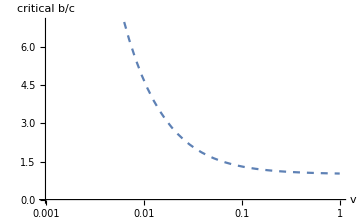

```mathematica
params={β->0.001,u->0.001,n->40};
expressions={ (zcalc[n,u,v]- hcalc[n,u,v])/(gcalc[n,u,v]- hcalc[n,u,v])}//FullSimplify
expressions={ (zcalc[n,u,v]- hcalc[n,u,v])/(gcalc[n,u,v]- hcalc[n,u,v])}/.params//FullSimplify;
LogLinearPlot[expressions,{v,0,1},PlotRange->{0,7},AxesLabel->{"v","critical b/c"},ImageSize->Medium,PlotStyle->Dashed]
```

Solve the condition for ν = N*v:

```mathematica
rules2 ={d_?NumericQ+μ->d,d_?NumericQ+f_?NumericQ μ->d,d_?NumericQ c+f_?NumericQ c μ->d c,d_+f_?NumericQ b c μ->d};
```

```mathematica
sol =Solve[b/c==(zeval[μ,ν]-heval[μ,ν])/(geval[μ,ν]-heval[μ,ν]) // FullSimplify, ν];
ν/.sol[[2]]//FullSimplify;
FullSimplify[ν/.sol[[2]]]//.rules2 (*μ->0 limit*)
FullSimplify[ν/.sol[[2]]] (*any μ*)
```

(-2 b+3 c+√(4 b^2-3 c^2))/(2 (b-c))

(3 c+2 c μ-b (2+μ)+√(2 b c μ+b^2 (2+μ)^2-c^2 (3+4 μ)))/(2 (b-c))

```mathematica
(*with parameters in our simulation*)
1/n(-2 b+3 c+√(4 b^2-3 c^2))/(2 (b-c))/.{b->1,c->0.2,n->40}(*μ->0 limit*)
1/n(3 c+2 c μ-b (2+μ)+√(2 b c μ+b^2 (2+μ)^2-c^2 (3+4 μ)))/(2 (b-c))/.{b->1,c->0.2,n->40,μ->40*0.001}(*any μ*)
```

0.00890268

0.00919936

### Critical thresholds: CC/CD

The critical threshold (b/c)* for CC to be favored / DD to be disfavored can be plotted as follows:

```mathematica
Clear[n,u,v,K,M]
```

{-(K n v (2+n (u+v))^2+M (3+n^2 (u+v)^2+n (4 u+3 v)))/((K-M) n v (2+n (u+v)))}

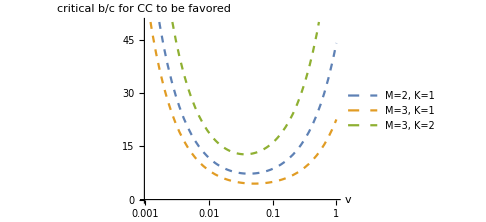

```mathematica
expressions2={ (zpcalc[n,u,v]- hpcalc[n,u,v])/(gpcalc[n,u,v]- hpcalc[n,u,v])}//FullSimplify
expressions2={ (zpcalc[n,u,v]- hpcalc[n,u,v])/(gpcalc[n,u,v]- hpcalc[n,u,v])}/.params//FullSimplify;
(*examples with K and M*)
LogLinearPlot[{expressions2/.{K->1,M->2},expressions2/.{K->1,M->3},expressions2/.{K->2,M->3}},
{v,0,1},PlotRange->{0,50},AxesLabel->{"v","critical b/c\nfor CC to\nbe favored"},ImageSize->Medium,PlotStyle->Dashed,
PlotLegends->{"M=2, K=1","M=3, K=1","M=3, K=2"}]
```

Solve the condition for ν = N*v:

```mathematica
rules3 ={d_?NumericQ+μ->d,d_?NumericQ+f_?NumericQ μ->d,d_?NumericQ+μ^2->d,e_?NumericQ+d_?NumericQ μ (c_?NumericQ+ν)->e};
```

```mathematica
FullSimplify[(zpeval[μ,ν]-hpeval[μ,ν])/(gpeval[μ,ν]-hpeval[μ,ν]) ]//.rules3
```

-(K ν (2+ν)^2+M (3+ν (3+ν)))/((K-M) ν (2+ν))

```mathematica
sol2 =Solve[b/c==(FullSimplify[(zpeval[μ,ν]-hpeval[μ,ν])/(gpeval[μ,ν]-hpeval[μ,ν]) ]//.rules3), ν];
(*TOO SLOW*)
(*ν/.sol2[[1]]//FullSimplify;*)
(*FullSimplify[ν/.sol[[2]]]//.rules2 (*μ->0 limit*)
FullSimplify[ν/.sol[[2]]] (*any μ*)*)
```

```mathematica
ν/40/.sol2/.{M->2,K->1,c->0.2,b->1} //Chop(*no solution in R_+, so CC cannot be favored*)
ν/40/.sol2/.{M->3,K->1,c->0.2,b->1} //Chop(*CC is favored for intermediate values of v*)
ν/40/.sol2/.{M->3,K->2,c->0.2,b->1} //Chop(*no solution in R_+, so CC cannot be favored*)
ν/40/.sol2/.{M->4,K->1,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->4,K->2,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->4,K->3,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->5,K->1,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->5,K->2,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->5,K->3,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->5,K->4,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->6,K->1,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->6,K->2,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->6,K->3,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->6,K->4,c->0.2,b->1} //Chop
ν/40/.sol2/.{M->6,K->5,c->0.2,b->1} //Chop
```

{0.0152347-0.0381841 ⅈ,-0.0554694,0.0152347+0.0381841 ⅈ}

{0.104057,-0.0540569,0.025}

{-0.0581739,-0.00841305+0.0337325 ⅈ,-0.00841305-0.0337325 ⅈ}

{0.212088,-0.0535861,0.0164981}

{0.0152347-0.0381841 ⅈ,-0.0554694,0.0152347+0.0381841 ⅈ}

{-0.0605425,-0.0155621+0.0281097 ⅈ,-0.0155621-0.0281097 ⅈ}

{0.314378,-0.0533515,0.0139738}

{0.0397644-0.0238305 ⅈ,-0.0545287,0.0397644+0.0238305 ⅈ}

{-0.0568528,-0.000740255+0.0370623 ⅈ,-0.000740255-0.0370623 ⅈ}

{-0.01875-0.0242061 ⅈ,-0.0625,-0.01875+0.0242061 ⅈ}

{0.41549,-0.053211,0.0127213}

{0.104057,-0.0540569,0.025}

{0.0152347-0.0381841 ⅈ,-0.0554694,0.0152347+0.0381841 ⅈ}

{-0.0581739,-0.00841305+0.0337325 ⅈ,-0.00841305-0.0337325 ⅈ}

{-0.0204605-0.0214287 ⅈ,-0.064079,-0.0204605+0.0214287 ⅈ}

### Summary: y, z, g, h, z’, g’, h’ for p < 1

In summary we have

```mathematica
yeval[μ,ν]
zeval[μ,ν]
geval[μ,ν]
heval[μ,ν]
```

(2+μ)/(2+2 μ)

K/(M+M ν)

K/(2 M (1+ν))+K/(2 M (1+μ+ν))

(3 K+K μ)/(2 M (2+μ) (1+ν))+K/(4 M (1+μ+ν))-(K μ (3+μ))/(4 M (1+μ) (2+μ) (3+μ+ν))

```mathematica
zpeval[μ,ν]
gpeval[μ,ν]
hpeval[μ,ν]
```

K^2/M^2+(-K^2+K M)/(M^2 (1+ν))

(K^2 (2+μ))/(2 M^2 (1+μ))-(K (K-M))/(2 M^2 (1+ν))-(K (K-M))/(2 M^2 (1+μ+ν))

(K^2 (2+μ))/(2 M^2 (1+μ))+(-3 K^2+3 K M-K^2 μ+K M μ)/(2 M^2 (2+μ) (1+ν))+(-K^2+K M)/(4 M^2 (1+μ+ν))+(3 K^2 μ-3 K M μ+K^2 μ^2-K M μ^2)/(4 M^2 (1+μ) (2+μ) (3+μ+ν))

## 3. Computing stationary strategy frequencies for p < 1

### Computing the full bracketed terms

We define the following functions to compute the original bracketed terms in (3):

```mathematica
Clear[nn,ββ,pp,bb,cc,μ,μμ,ν,νν];
ΔxCC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]:=xCCbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν],zp->zpeval[μ,ν],gp-> gpeval[μ,ν],hp-> hpeval[μ,ν]}/.{K->KK,M->MM};
ΔxCD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]:=
xCDbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν],z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]}/.{K->KK,M->MM};
ΔxDC[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]:=
xDCbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν],z->zeval[μ,ν],g-> geval[μ,ν],h-> heval[μ,ν]}/.{K->KK,M->MM};
ΔxDD[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]:=xDDbracket3/.{n->nn,b->bb,c->cc,y->yeval[μ,ν],zp->zpeval[μ,ν],gp-> gpeval[μ,ν],hp-> hpeval[μ,ν]}/.{K->KK,M->MM};
```

The full expressions are

```mathematica
FullSimplify[ΔxCC[n,b,c,β,p,μ,ν,K,M]] 
FullSimplify[ΔxCD[n,b,c,β,p,μ,ν,K,M]]
FullSimplify[ΔxDC[n,b,c,β,p,μ,ν,K,M]] 
FullSimplify[ΔxDD[n,b,c,β,p,μ,ν,K,M]]
```

-(K μ (b (K-M) ν (2+μ+ν)+c K ν (2+μ+ν)^2+c M (3+μ^2+2 μ (2+ν)+ν (3+ν))))/(8 M (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

(K μ (b ν (2+μ+ν)-c (3+μ^2+2 μ (2+ν)+ν (3+ν))))/(8 (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

(K μ (-b ν (2+μ+ν)+c (3+μ^2+2 μ (2+ν)+ν (3+ν))))/(8 (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

(K μ (b (K-M) ν (2+μ+ν)+c K ν (2+μ+ν)^2+c M (3+μ^2+2 μ (2+ν)+ν (3+ν))))/(8 M (1+μ) (1+ν) (1+μ+ν) (3+μ+ν))

In the limit μ -> 0, we have

```mathematica
rules={d_?NumericQ+μ->d,d_?NumericQ+d_ μ->d,d_?NumericQ + μ^2-> d,d_?NumericQ +f_?NumericQ μ*k_-> d};
ΔxCClim[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]=FullSimplify[ΔxCC[nn,bb,cc,ββ,pp,μ,ν,KK,MM]]//.rules;
ΔxCDlim[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]=FullSimplify[ΔxCD[nn,bb,cc,ββ,pp,μ,ν,KK,MM]]//.rules;
ΔxDClim[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]=FullSimplify[ΔxDC[nn,bb,cc,ββ,pp,μ,ν,KK,MM]]//.rules;
ΔxDDlim[nn_,bb_,cc_,ββ_,pp_,μ_,ν_,KK_,MM_]=FullSimplify[ΔxDD[nn,bb,cc,ββ,pp,μ,ν,KK,MM]]//.rules;

FullSimplify[ΔxCClim[n,b,c,β,p,μ,ν,K,M]] 
FullSimplify[ΔxCDlim[n,b,c,β,p,μ,ν,K,M]]
FullSimplify[ΔxDClim[n,b,c,β,p,μ,ν,K,M]] 
FullSimplify[ΔxDDlim[n,b,c,β,p,μ,ν,K,M]]

(*Check M=K case*)
FullSimplify[ΔxCClim[n,b,c,β,p,μ,ν,M,M]]
```

-(K μ (b (K-M) ν (2+ν)+c K ν (2+ν)^2+c M (3+ν (3+ν))))/(8 M (1+ν)^2 (3+ν))

(K μ (b ν (2+ν)-c (3+ν (3+ν))))/(8 (1+ν)^2 (3+ν))

(K μ (-b ν (2+ν)+c (3+ν (3+ν))))/(8 (1+ν)^2 (3+ν))

(K μ (b (K-M) ν (2+ν)+c K ν (2+ν)^2+c M (3+ν (3+ν))))/(8 M (1+ν)^2 (3+ν))

-1/8 c M μ

### Plot changes due to selection

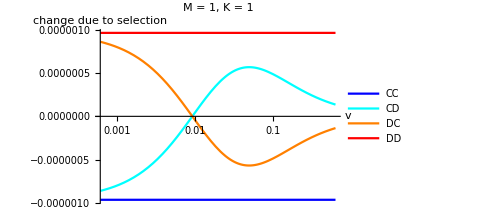
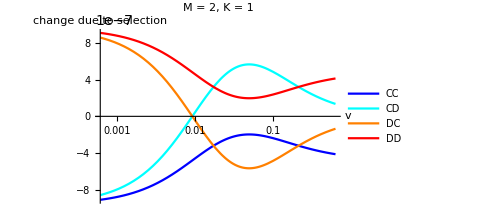
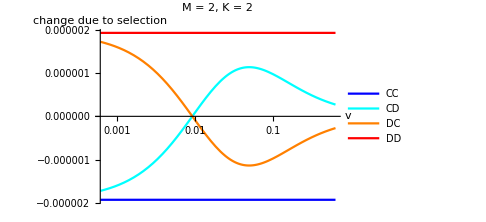
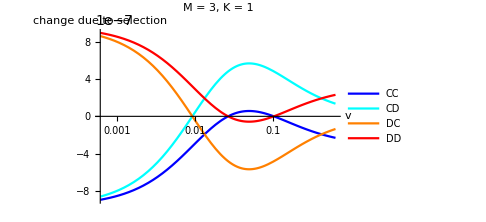
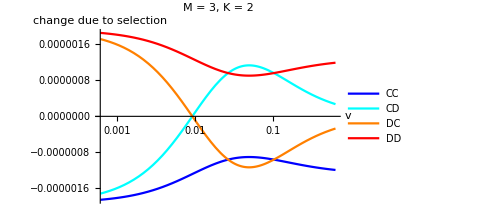
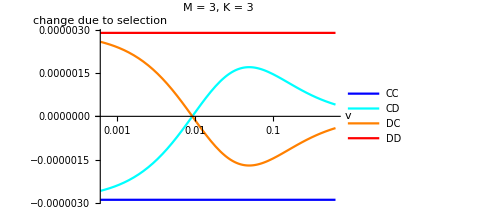

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν,KK,MM];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

Table[{
LogLinearPlot[{
ββ*ΔxCC[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxCD[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxDC[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxDD[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},
PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},
PlotLabel->"M = "<>ToString[MM]<>", K = "<>ToString[KK],
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}]},
{MM,1,3},{KK,1,MM}
]//Flatten[#,3] &
```

In the limit μ -> 0,

```mathematica
ΔxCClim[n,b,c,β,p,μ,n*v,K,M]/.{n->40,u->0.001,β->0.001,b->1.0,c->0.2}/.{μ->40*0.001,K->1,M->3}
```

-(0.00166667 (-80. v (2+40 v)+8. v (2+40 v)^2+0.6 (3+40 v (3+40 v))))/((1+40 v)^2 (3+40 v))

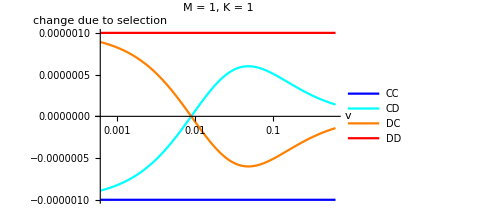
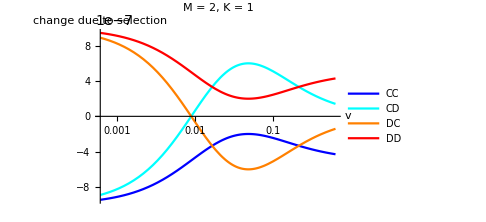
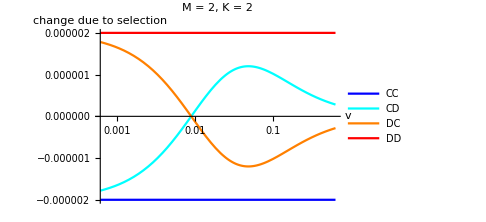
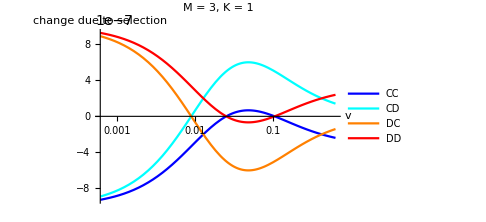
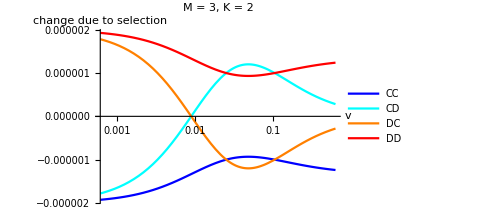
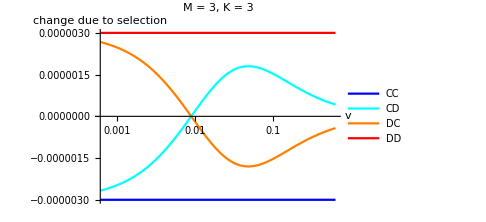

```mathematica
Table[{
LogLinearPlot[{
ββ*ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxDClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
ββ*ΔxDDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM]},{vv,0,0.625},
AxesLabel->{"v","change due to selection"},
PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},Automatic},
PlotLabel->"M = "<>ToString[MM]<>", K = "<>ToString[KK],
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}]},
{MM,1,3},{KK,1,MM}
]//Flatten[#,3] &
```

### Plot relative abundances of strategies

See the SI for the derivation of the expressions plotted below.

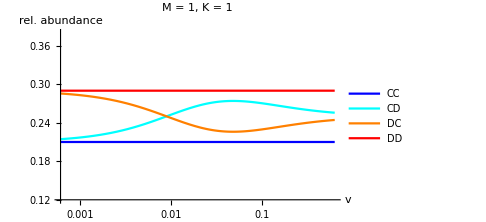
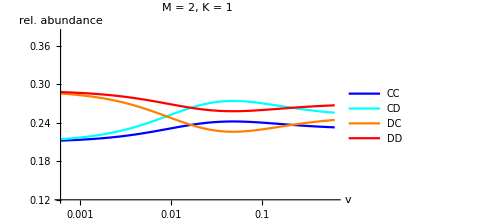
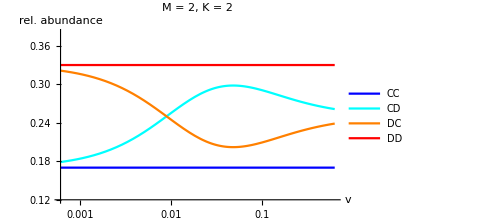
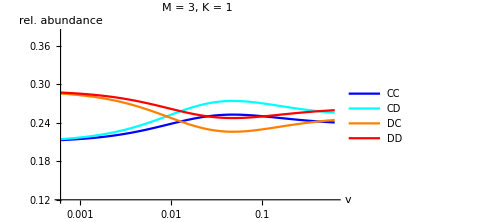
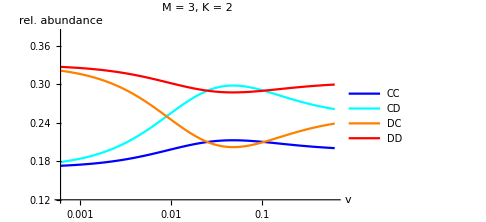
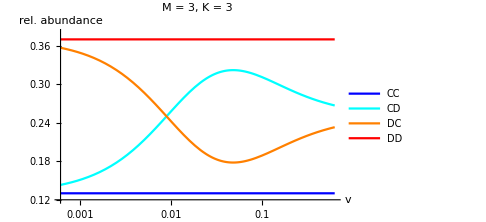

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;

Table[{
LogLinearPlot[{
1/4+(nn ββ(1-uu))/uu ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
1/4+(nn ββ(1-uu))/uu ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
1/4+(nn ββ(1-uu))/uu ΔxDClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM],
1/4+(nn ββ(1-uu))/uu ΔxDDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,MM]},{vv,0,0.625},
AxesLabel->{"v","rel. abundance"},
PlotLegends->{"CC","CD","DC","DD"},
PlotRange->{{0,0.625},{0.12,0.38}},
PlotLabel->"M = "<>ToString[MM]<>", K = "<>ToString[KK],
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red}]},
{MM,1,3},{KK,1,MM}
]//Flatten[#,3] &
```

### Export data

```mathematica
Clear[n,β,p,u,v,params,ΔxCClimFull,ΔxCDlimFull,ΔxDClimFull,ΔxDDlimFull];
params={n->40,u->0.001,β->0.001,b->1.0,c->0.2}; (*note that pe is not needed*)

vs=Table[10^log10v,{log10v,-3,Log10[0.625],(Log10[0.005] - Log10[0.001])/2/2}];
Ms=Table[M,{M,1,3}];

data=Flatten[
Table[{M,K,u/.params,v,
(1/4+(n β(1-u))/u ΔxCClim[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxCDlim[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxDClim[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxDDlim[n,b,c,β,p,n*u,n*v,K,M])/.params},{M,1,3},{K,1,M},{v,vs}],
2];
headers={"M","K","u","v","CC","CD","DC","DD"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_strat_mu-small.csv"; (*change as needed*)
(*Export[filename,data]*)

data=Flatten[
Table[{M,K,u/.params,v,
(1/4+(n β(1-u))/u ΔxCC[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxCD[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxDC[n,b,c,β,p,n*u,n*v,K,M])/.params,
(1/4+(n β(1-u))/u ΔxDD[n,b,c,β,p,n*u,n*v,K,M])/.params},{M,1,3},{K,1,M},{v,vs}],
2];
headers={"M","K","u","v","CC","CD","DC","DD"};
data=Prepend[data,headers];

filename="~/.julia/dev/CooperationPolarization2/analytics/calc_data_strat_mu-any.csv"; (*change as needed*)
(*Export[filename,data]*)
```

```mathematica
data//MatrixForm
```

(M | K | u | v | CC | CD | DC | DD
1 | 1 | 0.001 | 0.001 | 0.211577 | 0.218119 | 0.281881 | 0.288423
1 | 1 | 0.001 | 0.00149535 | 0.211577 | 0.22106 | 0.27894 | 0.288423
1 | 1 | 0.001 | 0.00223607 | 0.211577 | 0.225126 | 0.274874 | 0.288423
1 | 1 | 0.001 | 0.0033437 | 0.211577 | 0.230551 | 0.269449 | 0.288423
1 | 1 | 0.001 | 0.005 | 0.211577 | 0.237427 | 0.262573 | 0.288423
1 | 1 | 0.001 | 0.00747674 | 0.211577 | 0.245538 | 0.254462 | 0.288423
1 | 1 | 0.001 | 0.0111803 | 0.211577 | 0.254211 | 0.245789 | 0.288423
1 | 1 | 0.001 | 0.0167185 | 0.211577 | 0.262312 | 0.237688 | 0.288423
1 | 1 | 0.001 | 0.025 | 0.211577 | 0.268551 | 0.231449 | 0.288423
1 | 1 | 0.001 | 0.0373837 | 0.211577 | 0.272001 | 0.227999 | 0.288423
1 | 1 | 0.001 | 0.0559017 | 0.211577 | 0.272503 | 0.227497 | 0.288423
1 | 1 | 0.001 | 0.0835925 | 0.211577 | 0.270662 | 0.229338 | 0.288423
1 | 1 | 0.001 | 0.125 | 0.211577 | 0.267465 | 0.232535 | 0.288423
1 | 1 | 0.001 | 0.186919 | 0.211577 | 0.26385 | 0.23615 | 0.288423
1 | 1 | 0.001 | 0.279508 | 0.211577 | 0.260464 | 0.239536 | 0.288423
1 | 1 | 0.001 | 0.417963 | 0.211577 | 0.257626 | 0.242374 | 0.288423
1 | 1 | 0.001 | 0.625 | 0.211577 | 0.255414 | 0.244586 | 0.288423
2 | 1 | 0.001 | 0.001 | 0.214848 | 0.218119 | 0.281881 | 0.285152
2 | 1 | 0.001 | 0.00149535 | 0.216318 | 0.22106 | 0.27894 | 0.283682
2 | 1 | 0.001 | 0.00223607 | 0.218352 | 0.225126 | 0.274874 | 0.281648
2 | 1 | 0.001 | 0.0033437 | 0.221064 | 0.230551 | 0.269449 | 0.278936
2 | 1 | 0.001 | 0.005 | 0.224502 | 0.237427 | 0.262573 | 0.275498
2 | 1 | 0.001 | 0.00747674 | 0.228558 | 0.245538 | 0.254462 | 0.271442
2 | 1 | 0.001 | 0.0111803 | 0.232894 | 0.254211 | 0.245789 | 0.267106
2 | 1 | 0.001 | 0.0167185 | 0.236945 | 0.262312 | 0.237688 | 0.263055
2 | 1 | 0.001 | 0.025 | 0.240064 | 0.268551 | 0.231449 | 0.259936
2 | 1 | 0.001 | 0.0373837 | 0.241789 | 0.272001 | 0.227999 | 0.258211
2 | 1 | 0.001 | 0.0559017 | 0.24204 | 0.272503 | 0.227497 | 0.25796
2 | 1 | 0.001 | 0.0835925 | 0.24112 | 0.270662 | 0.229338 | 0.25888
2 | 1 | 0.001 | 0.125 | 0.239521 | 0.267465 | 0.232535 | 0.260479
2 | 1 | 0.001 | 0.186919 | 0.237713 | 0.26385 | 0.23615 | 0.262287
2 | 1 | 0.001 | 0.279508 | 0.23602 | 0.260464 | 0.239536 | 0.26398
2 | 1 | 0.001 | 0.417963 | 0.234601 | 0.257626 | 0.242374 | 0.265399
2 | 1 | 0.001 | 0.625 | 0.233495 | 0.255414 | 0.244586 | 0.266505
2 | 2 | 0.001 | 0.001 | 0.173154 | 0.186239 | 0.313761 | 0.326846
2 | 2 | 0.001 | 0.00149535 | 0.173154 | 0.19212 | 0.30788 | 0.326846
2 | 2 | 0.001 | 0.00223607 | 0.173154 | 0.200253 | 0.299747 | 0.326846
2 | 2 | 0.001 | 0.0033437 | 0.173154 | 0.211103 | 0.288897 | 0.326846
2 | 2 | 0.001 | 0.005 | 0.173154 | 0.224854 | 0.275146 | 0.326846
2 | 2 | 0.001 | 0.00747674 | 0.173154 | 0.241077 | 0.258923 | 0.326846
2 | 2 | 0.001 | 0.0111803 | 0.173154 | 0.258422 | 0.241578 | 0.326846
2 | 2 | 0.001 | 0.0167185 | 0.173154 | 0.274624 | 0.225376 | 0.326846
2 | 2 | 0.001 | 0.025 | 0.173154 | 0.287103 | 0.212897 | 0.326846
2 | 2 | 0.001 | 0.0373837 | 0.173154 | 0.294002 | 0.205998 | 0.326846
2 | 2 | 0.001 | 0.0559017 | 0.173154 | 0.295006 | 0.204994 | 0.326846
2 | 2 | 0.001 | 0.0835925 | 0.173154 | 0.291324 | 0.208676 | 0.326846
2 | 2 | 0.001 | 0.125 | 0.173154 | 0.284929 | 0.215071 | 0.326846
2 | 2 | 0.001 | 0.186919 | 0.173154 | 0.2777 | 0.2223 | 0.326846
2 | 2 | 0.001 | 0.279508 | 0.173154 | 0.270928 | 0.229072 | 0.326846
2 | 2 | 0.001 | 0.417963 | 0.173154 | 0.265252 | 0.234748 | 0.326846
2 | 2 | 0.001 | 0.625 | 0.173154 | 0.260827 | 0.239173 | 0.326846
3 | 1 | 0.001 | 0.001 | 0.215939 | 0.218119 | 0.281881 | 0.284061
3 | 1 | 0.001 | 0.00149535 | 0.217899 | 0.22106 | 0.27894 | 0.282101
3 | 1 | 0.001 | 0.00223607 | 0.22061 | 0.225126 | 0.274874 | 0.27939
3 | 1 | 0.001 | 0.0033437 | 0.224227 | 0.230551 | 0.269449 | 0.275773
3 | 1 | 0.001 | 0.005 | 0.22881 | 0.237427 | 0.262573 | 0.27119
3 | 1 | 0.001 | 0.00747674 | 0.234218 | 0.245538 | 0.254462 | 0.265782
3 | 1 | 0.001 | 0.0111803 | 0.24 | 0.254211 | 0.245789 | 0.26
3 | 1 | 0.001 | 0.0167185 | 0.2454 | 0.262312 | 0.237688 | 0.2546
3 | 1 | 0.001 | 0.025 | 0.24956 | 0.268551 | 0.231449 | 0.25044
3 | 1 | 0.001 | 0.0373837 | 0.25186 | 0.272001 | 0.227999 | 0.24814
3 | 1 | 0.001 | 0.0559017 | 0.252194 | 0.272503 | 0.227497 | 0.247806
3 | 1 | 0.001 | 0.0835925 | 0.250967 | 0.270662 | 0.229338 | 0.249033
3 | 1 | 0.001 | 0.125 | 0.248835 | 0.267465 | 0.232535 | 0.251165
3 | 1 | 0.001 | 0.186919 | 0.246426 | 0.26385 | 0.23615 | 0.253574
3 | 1 | 0.001 | 0.279508 | 0.244168 | 0.260464 | 0.239536 | 0.255832
3 | 1 | 0.001 | 0.417963 | 0.242276 | 0.257626 | 0.242374 | 0.257724
3 | 1 | 0.001 | 0.625 | 0.240801 | 0.255414 | 0.244586 | 0.259199
3 | 2 | 0.001 | 0.001 | 0.177515 | 0.186239 | 0.313761 | 0.322485
3 | 2 | 0.001 | 0.00149535 | 0.179476 | 0.19212 | 0.30788 | 0.320524
3 | 2 | 0.001 | 0.00223607 | 0.182187 | 0.200253 | 0.299747 | 0.317813
3 | 2 | 0.001 | 0.0033437 | 0.185804 | 0.211103 | 0.288897 | 0.314196
3 | 2 | 0.001 | 0.005 | 0.190387 | 0.224854 | 0.275146 | 0.309613
3 | 2 | 0.001 | 0.00747674 | 0.195795 | 0.241077 | 0.258923 | 0.304205
3 | 2 | 0.001 | 0.0111803 | 0.201577 | 0.258422 | 0.241578 | 0.298423
3 | 2 | 0.001 | 0.0167185 | 0.206977 | 0.274624 | 0.225376 | 0.293023
3 | 2 | 0.001 | 0.025 | 0.211137 | 0.287103 | 0.212897 | 0.288863
3 | 2 | 0.001 | 0.0373837 | 0.213436 | 0.294002 | 0.205998 | 0.286564
3 | 2 | 0.001 | 0.0559017 | 0.213771 | 0.295006 | 0.204994 | 0.286229
3 | 2 | 0.001 | 0.0835925 | 0.212544 | 0.291324 | 0.208676 | 0.287456
3 | 2 | 0.001 | 0.125 | 0.210412 | 0.284929 | 0.215071 | 0.289588
3 | 2 | 0.001 | 0.186919 | 0.208003 | 0.2777 | 0.2223 | 0.291997
3 | 2 | 0.001 | 0.279508 | 0.205745 | 0.270928 | 0.229072 | 0.294255
3 | 2 | 0.001 | 0.417963 | 0.203853 | 0.265252 | 0.234748 | 0.296147
3 | 2 | 0.001 | 0.625 | 0.202378 | 0.260827 | 0.239173 | 0.297622
3 | 3 | 0.001 | 0.001 | 0.134731 | 0.154358 | 0.345642 | 0.365269
3 | 3 | 0.001 | 0.00149535 | 0.134731 | 0.163179 | 0.336821 | 0.365269
3 | 3 | 0.001 | 0.00223607 | 0.134731 | 0.175379 | 0.324621 | 0.365269
3 | 3 | 0.001 | 0.0033437 | 0.134731 | 0.191654 | 0.308346 | 0.365269
3 | 3 | 0.001 | 0.005 | 0.134731 | 0.212281 | 0.287719 | 0.365269
3 | 3 | 0.001 | 0.00747674 | 0.134731 | 0.236615 | 0.263385 | 0.365269
3 | 3 | 0.001 | 0.0111803 | 0.134731 | 0.262633 | 0.237367 | 0.365269
3 | 3 | 0.001 | 0.0167185 | 0.134731 | 0.286936 | 0.213064 | 0.365269
3 | 3 | 0.001 | 0.025 | 0.134731 | 0.305654 | 0.194346 | 0.365269
3 | 3 | 0.001 | 0.0373837 | 0.134731 | 0.316002 | 0.183998 | 0.365269
3 | 3 | 0.001 | 0.0559017 | 0.134731 | 0.31751 | 0.18249 | 0.365269
3 | 3 | 0.001 | 0.0835925 | 0.134731 | 0.311987 | 0.188013 | 0.365269
3 | 3 | 0.001 | 0.125 | 0.134731 | 0.302394 | 0.197606 | 0.365269
3 | 3 | 0.001 | 0.186919 | 0.134731 | 0.29155 | 0.20845 | 0.365269
3 | 3 | 0.001 | 0.279508 | 0.134731 | 0.281392 | 0.218608 | 0.365269
3 | 3 | 0.001 | 0.417963 | 0.134731 | 0.272877 | 0.227123 | 0.365269
3 | 3 | 0.001 | 0.625 | 0.134731 | 0.266241 | 0.233759 | 0.365269)

## 4. Miscellaneous analysis

### Plot critical b/c for CC/DD

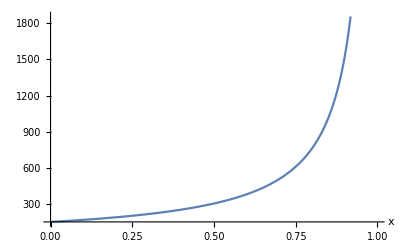

{}

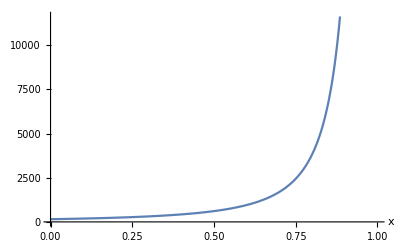

```mathematica
Plot[(x*v(v+2)^2+(v(v+3)+3))/((1-x)v(v+2))/.{v->0.01},{x,0,1},PlotRange->{{0,1},Automatic},AxesLabel->Automatic]
Solve[(2+v)/(1-x)+(3+v (3+v)+v (2+v)^2 x)/(v (2+v) (1-x)^2)==0,x]
Plot[((2+v)/(1-x)+(3+v (3+v)+v (2+v)^2 x)/(v (2+v) (1-x)^2))/.{v->0.01},{x,0,1},PlotRange->{{0,1},Automatic},AxesLabel->Automatic]
```

### Plot CC+CD

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;


p6 = LogLinearPlot[{
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,1]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,1]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,2]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,2]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,3]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,3]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,4]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,4]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 1, K = 1","M = 2, K = 1","M = 3, K = 1","M = 4, K = 1","M = 5, K = 1"},
(*PlotRange->{{0,0.625},{0.4,0.55}},*)
PlotLabel->"CC + CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p4 = LogLinearPlot[{
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,1]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,2]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,3]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,4]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 1, K = 1","M = 2, K = 1","M = 3, K = 1","M = 4, K = 1","M = 5, K = 1"},
(*PlotRange->{{0,0.625},{0.4,0.55}},*)
PlotLabel->"CC",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p5 = LogLinearPlot[{
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,1]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,2]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,3]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,4]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 1, K = 1","M = 2, K = 1","M = 3, K = 1","M = 4, K = 1","M = 5, K = 1"},
(*PlotRange->{{0,0.625},{0.4,0.55}},*)
PlotLabel->"CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p3=LogLinearPlot[{
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,5]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,5]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,5]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,5,5]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,5,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 5, K = 1","M = 5, K = 2","M = 5, K = 3","M = 5, K = 4","M = 5, K = 5"},
(*PlotRange->{{0,0.625},{0.1,0.65}},*)
PlotLabel->"CC + CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p1=LogLinearPlot[{
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,5,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 5, K = 1","M = 5, K = 2","M = 5, K = 3","M = 5, K = 4","M = 5, K = 5"},
(*PlotRange->{{0,0.625},{0.1,0.65}},*)
PlotLabel->"CC",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p2=LogLinearPlot[{
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,5]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,5,5])},{vv,0,0.625},
AxesLabel->{"v","frequency"},
PlotLegends->{"M = 5, K = 1","M = 5, K = 2","M = 5, K = 3","M = 5, K = 4","M = 5, K = 5"},
(*PlotRange->{{0,0.625},{0.1,0.65}},*)
PlotLabel->"CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
```

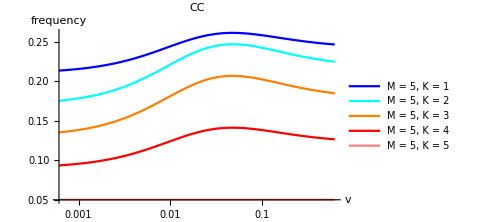
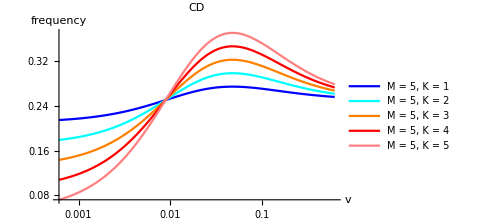
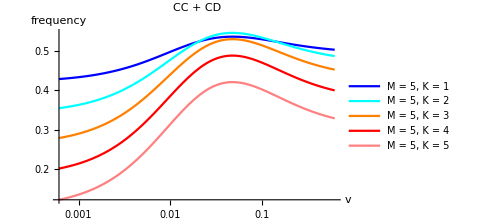

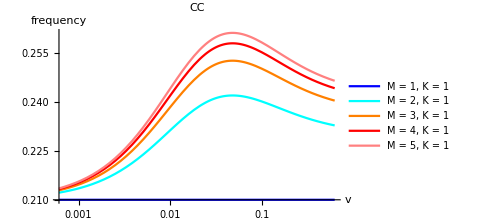
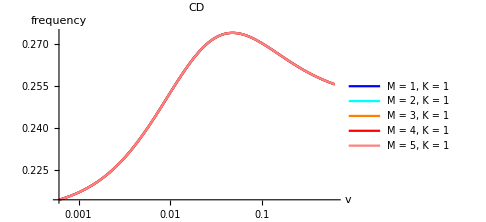
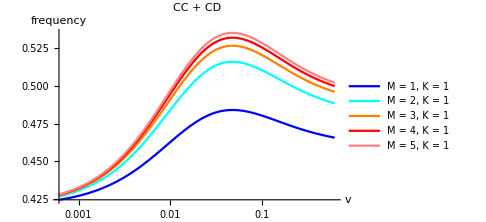

```mathematica
{p1,p2,p3}
{p4,p5,p6}
```

### Plot CC vs M or K

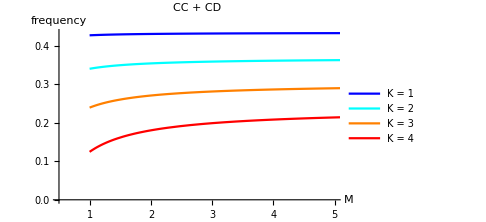
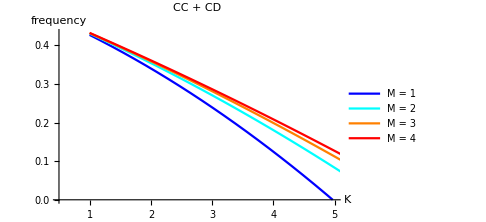

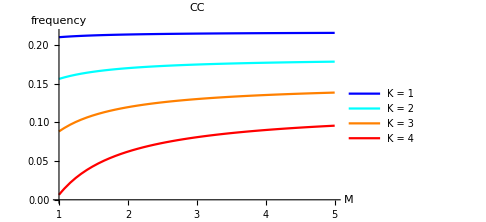
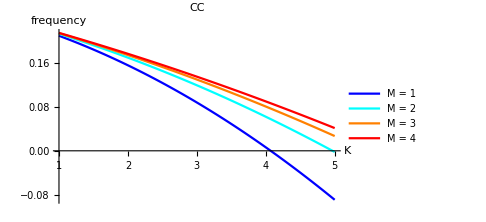

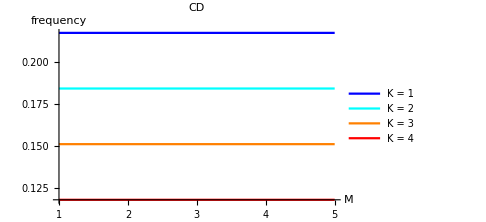
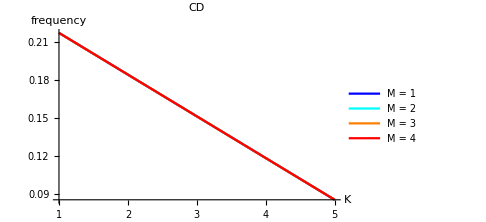

```mathematica
Clear[nn,ββ,pp,bb,cc,μμ,νν,KK,MM,vv];
nn=40;uu=0.001;pp=0;ββ=0.001;cc=0.2;bb=1.0;μμ=nn*uu;vv=0.001;

p7 =Plot[{
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,MM]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,MM]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,MM]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,MM]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,MM]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,MM]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,MM]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,MM])
},{MM,1,10},
AxesLabel->{"M","frequency"},
PlotLegends->{"K = 1","K = 2","K = 3", "K = 4"},
PlotRange->{{0.5,5},{0, Automatic}},
PlotLabel->"CC + CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p8 =Plot[{
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,1]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,1]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,2]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,2]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,3]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,3]),
1/2+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,4]+ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,4])
},{KK,1,10},
AxesLabel->{"K","frequency"},
PlotLegends->{"M = 1","M = 2","M = 3", "M = 4"},
PlotRange->{{0.5,5},{0, Automatic}},
PlotLabel->"CC + CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p9 =Plot[{
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,MM])
},{MM,1,5},
AxesLabel->{"M","frequency"},
PlotLegends->{"K = 1","K = 2","K = 3", "K = 4"},
(*PlotRange->{{0.5,5},{0, Automatic}},*)
PlotLabel->"CC",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p10 =Plot[{
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,1]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,2]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,3]),
1/4+(nn ββ(1-uu))/uu(ΔxCClim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,4])
},{KK,1,5},
AxesLabel->{"K","frequency"},
PlotLegends->{"M = 1","M = 2","M = 3", "M = 4"},
(*PlotRange->{{0.5,5},{0, Automatic}},*)
PlotLabel->"CC",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p11 =Plot[{
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,1,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,2,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,3,MM]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,4,MM])
},{MM,1,5},
AxesLabel->{"M","frequency"},
PlotLegends->{"K = 1","K = 2","K = 3", "K = 4"},
(*PlotRange->{{0.5,5},{0, Automatic}},*)
PlotLabel->"CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
p12 =Plot[{
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,1]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,2]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,3]),
1/4+(nn ββ(1-uu))/uu(ΔxCDlim[nn,bb,cc,ββ,pp,μμ,nn*vv,KK,4])
},{KK,1,5},
AxesLabel->{"K","frequency"},
PlotLegends->{"M = 1","M = 2","M = 3", "M = 4"},
(*PlotRange->{{0.5,5},{0, Automatic}},*)
PlotLabel->"CD",
ImageSize->Medium,PlotStyle->{Blue,Cyan,Orange,Red,Pink}];
{p7,p8}
{p9,p10}
{p11,p12}
```

### Rewriting changes due to selection to improve interpretability

Define intermediate functions:

```mathematica
R[ν_,b_,c_]:=(b ν (2+ν)-c (3+ν (3+ν)))/(8  (1+ν)^2 (3+ν))
S[ν_,b_,c_]:=(ν (2+ν) (b+c (2+ν)))/(8 (1+ν)^2 (3+ν))
```

```mathematica
FullSimplify[ΔxCClim[n,b,c,β,p,μ,ν,K,M]]==μ K R[ν,b,c]-(μ K^2)/M S[ν,b,c]//FullSimplify
FullSimplify[ΔxCDlim[n,b,c,β,p,μ,ν,K,M]]==μ K R[ν,b,c]//FullSimplify
(FullSimplify[ΔxCClim[n,b,c,β,p,μ,ν,K,M]]-FullSimplify[ΔxCDlim[n,b,c,β,p,μ,ν,K,M]])==-(μ K^2)/M S[ν,b,c]//FullSimplify
```

True

True

True

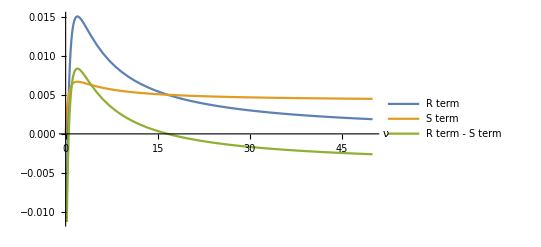

```mathematica
params={b->1,c->0.2,M->6,K->1,μ->40*0.001};
Plot[{R[ν,b,c]/.params,K/M S[ν,b,c]/.params,R[ν,b,c]-K/M S[ν,b,c]/.params},{ν,0,50},AxesLabel->Automatic,PlotLegends->{"R term","S term","R term - S term"}]
```